Термодинамический анализ газового цикла

Дано:
Сухой воздух массой 1 кг совершает прямой термодинамический цикл, состоящий
из четырех последовательных термодинамических процессов, параметры которых
определяются преподавателем.

Требуется:
1) рассчитать давление (p), удельный объем (v) и температуру (T) воздуха для
основных точек цикла,
2) определить для каждого из процессов значения показателей политропы (n) и
теплоемкости (c), вычислить изменение внутренней энергии (Δu), энтальпии (Δh),
энтропии (Δs), теплоту процесса (q), работу процесса (l) и располагаемую работу (l_0),
3) определить суммарные количества подведенной (q’) и отведенной (q’’) теплоты,
работу цикла (l_ц), располагаемую работу цикла (l_(0ц)) и термический к.п.д. цикла (η_t).
4) построить цикл в координатах:
а) lg v –lg p,
б) v –p, используя предыдущее построение для нахождения трех или четырех
промежуточных точек на каждом из процессов,
в) s –Т, нанеся основные точки цикла и составляющие его процессы,
5) для одного из процессов цикла, кроме изотермического, привести схему его
графического расчета по тепловой s– диаграмме, изобразив на схеме линию процесса
вспомогательные линии изохорного и изобарного процессов, значения температур в
начале и в конце процесса, отрезки, соответствующие изменению энтропии в основном и 
вспомогательных процессах, площади, соответствующие теплоте процесса, изменению
внутренней энергии и энтальпии.

Дано:

-Graphics-

p_1=0.2 МПа
p_2=1.2 МПа
v_1=0.45 м^3/кг
T_3=573K   (t_3=300°C)
теплоёмкости процессов:
c_p=1.025  кДж/(кг К)
с_v=0.738 кДж/(кг К)
R=287 Дж/(кг К)
k=1.389

```mathematica
p={0,0,0,0};
v={0,0,0,0};
T={0,0,0,0};
p[[1]]=0.2 10^6;
p[[2]]=1.2 10^6;
v[[1]]=0.45;
T[[3]]=573;
R=287;
k=1.389;
cp=1025;
cv=cp-R;
```

1. Определить параметры p, v и T воздуха для основных точек цикла:

a) Для точки 1:

Используем уравнение состояния:

T_1=p_1 v_1/R=313.5К

```mathematica
T[[1]]=p[[1]] v[[1]]/R
```

313.589

б) Для точки 2:

Используем уравнение адиабаты и уравнение Клапейрона-Менделеева:

v_2=(v_1(p_1/p_2))^(1/k)
T_2=p_2 v_2/R
отсюда: v_2=0.123 м^3/кг
T_2=517.9K

```mathematica
v[[2]]=v[[1]] (p[[1]]/p[[2]])^(1/k)
T[[2]]=p[[2]]v[[2]]/R
```

0.123876

517.95

в) Для точки 3:

v_3=v_2=0.125 м^3/кг   т.к. процесс 2-3 изохорный.

Отсюда, из уравнения состояния получаем:

p_3=R T_3/v_3=1.32МПа

```mathematica
v[[3]]=v[[2]]
p[[3]]=R T[[3]]/v[[3]]
```

0.123876

1.32754×10^6

г) Для точки 4:

p_4=p_1=0.2 МПа т.к. процесс 4-1 изобарный

Используем уравнение адиабаты и уравнение состояния:

v_4=(v_3(p_3/p_4))^(1/k)
T_4=p_4 v_4/R
отсюда получаем:
v_4=0.48м^3/кг 
T_4=337.2 К

```mathematica
p[[4]]=p[[1]]
v[[4]]=v[[3]](p[[3]]/p[[4]])^(1/k)
T[[4]]=p[[4]]v[[4]]/R
```

200000.

0.483943

337.242

Результаты расчета сведем в таблицу:

```mathematica
names={"Параметр\nТочка","1","2","3","4"};
Grid[{names,Join[{"P, Па"},p],Join[{"V, (:043c)^3/кг"},v],Join[{"T, K"},T]}ᵀ,Frame->All,Spacings->{1, 1}]
```

Параметр
Точка | P, Па | V, м^3/кг | T, K
1 | 200000. | 0.45 | 313.589
2 | 1.2×10^6 | 0.123876 | 517.95
3 | 1.32754×10^6 | 0.123876 | 573
4 | 200000. | 0.483943 | 337.242

2) определить для каждого из процессов значения показателей политропы (n) и теплоемкости (c), вычислить изменение внутренней энергии (Δu), энтальпии (Δh), энтропии (Δs), теплоту процесса (q), работу процесса (l) и располагаемую работу (l_0):

Дадим характеристику процессам:

2-1  адиабатный 
3-2 изохорный
4-3 адиабатный
1-4 изобарный

```mathematica
cv
cp
k
```

{718.7,757.6,757.6,718.7}

{1005.7,1044.6,1044.6,1005.7}

{1.399,1.379,1.379,1.399}

Расчет будем проводить в векторном виде:

Показатели политропы определим по следующей формуле:

n_i=(lg (p_(i+1))/p_i)/(lg (v_(i+1))/v_i) 
тогда получим следующий результат:
n={1.389,∞,1.389,0.}, что есть ничто иное как:
n_(2-1)=1.389,n_(3-2)=∞,n_(4-3)=1.389,n_(1-4)=0

```mathematica
n=Table[-Log10[p[[If[i==4,1,i+1]]]/p[[i]]]/Log10[v[[If[i==4,1,i+1]]]/v[[i]]],{i,{1,2,3,4}}];
n[[2]]=Infinity;
n
```

Power::infy: Infinite expression 1/0. encountered.

{1.389,∞,1.389,0.}

Теплоемкости процессов, если их рассматривать как частные случаи политропного процесса, определим по формуле:

с=c_v (n-k)/(n-1), 
и получим следующий результат:
с={0,738,0,1025}, или по другому:
с_(2-1)=0,с_(3-2)=738 Дж/(кг К),с_(4-3)=0,с_(1-4)=1025 Дж/(кг К)

```mathematica
c=cv(n-k)/(n-1)//Chop;
c[[2]]=cv;
c[[4]]=cp;
c
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

{0,738,0,1025}

Изменение внутренней энергии определим по формуле:

Δu=c_v ΔT=c_v(T_(i+1)-T_i),
тогда получим:
Δu={150818.,40626.9,-173989.,-17456.3}
Δu_(2-1)=150818. Дж/кг,Δu_(3-2)=40626.9 Дж/кг,Δu_(4-3)=-173989. Дж/кг,Δu_(1-4)=-17456.3 Дж/кг

```mathematica
du=Table[cv(T[[If[i==4,1,i+1]]]-T[[i]]),{i,1,4}]
```

{150818.,40626.9,-173989.,-17456.3}

Изменение энтальпии идеального газа определим по формулам:

Δh=c_p ΔT=c_p(T_(i+1)-T_i),
тогда получим:
Δh={209470.,56426.3,-241652.,-24244.9}
Δh_(2-1)=209470. Дж/кг,Δh_(3-2)=56426.3 Дж/кг,Δh_(4-3)=-241652. Дж/кг,Δh_(1-4)=-24244.9 Дж/кг

```mathematica
dh=Table[cp(T[[If[i==4,1,i+1]]]-T[[i]]),{i,1,4}]
```

{209470.,56426.3,-241652.,-24244.9}

Изменение энтропии в рассматриваемых процессах определим по формуле:

Δs=c_p ln (v_(i+1))/v_i+c_v ln (p_(i+1))/p_i=ln ((v_(i+1))/v_i)^c_p((p_(i+1))/p_i)^c_v
тогда получим:
Δs={0,74.5433,0,-74.5373}
Δs_(2-1)=0,Δs_(3-2)=74.54 Дж/(кг K),Δs_(4-3)=0,Δs_(1-4)=-74.54 Дж/(кг K)

```mathematica
ds=Table[Log[ (v[[If[i==4,1,i+1]]]/v[[i]])^cp(p[[If[i==4,1,i+1]]]/p[[i]])^cv],{i,1,4}];
ds[[1]]=ds[[3]]=0;
ds[[4]]=-ds[[2]];
ds
```

{0,74.5433,0,-74.5433}

Теплоту процессов можно определить по формуле:

q=c ΔT=c_i (T_(i+1)-T_i)
тогда получим:
q={0.,40626.9,0.,-24244.9},или:
q_(2-1)=0,q_(3-2)=40626.9 Дж/кг,q_(4-3)=0,q_(1-4)=-24244.9 Дж/кг

```mathematica
q=Table[c[[i]](T[[If[i==4,1,i+1]]]-T[[i]]),{i,1,4}]
```

{0.,40626.9,0.,-24244.9}

Работу процессов определим из уравнений первого закона термодинамики:

l_i=q_i-Δu_i,
получим:
l={-150818.,0.,173989.,-6788.58},или:
l_(2-1)=-150818 Дж/кг,l_(3-2)=0,l_(4-3)=173989. Дж/кг,l_(1-4)=-6788.58 Дж/кг

```mathematica
l=q-du
```

{-150818.,0.,173989.,-6788.58}

Располагаемую работу определим также из первого закона термодинамики:

l_(0i)=q_i-Δh_i,
получим:
l_0={-209470.,-15799.4,241652.,0.}, или:
l_(2-1)=-209470 Дж/кг,l_(3-2)=-15799.4,l_(4-3)=241652 Дж/кг,l_(1-4)=0.

```mathematica
l0=q-dh
```

{-209470.,-15799.4,241652.,0.}

Результаты расчета сведем в таблицу:

```mathematica
names2={"Парам,\nПроц","n","c, (:0414:0436)/(:043a:0433 :041a)","Δu, (:0414:0436)/(:043a:0433)", "Δh, (:0414:0436)/(:043a:0433)","Δs, (:0414:0436)/(:043a:0433 :041a)","q, (:0414:0436)/(:043a:0433)", "l, (:0414:0436)/(:043a:0433)","l_0, (:0414:0436)/(:043a:0433)"};
Grid[Append[Prepend[Map[Flatten,{{"1-2","2-3","3-4","4-1"},{n,c,du,dh,ds,q,l,l0}ᵀ}ᵀ],names2],{"Σ","-","-",Total[du],Total[dh],Total[ds],Total[q],Total[l],Total[l0]}],Frame->All,Spacings->{1, 1}]
```

Парам,
Проц | n | c, Дж/(кг К) | Δu, Дж/кг | Δh, Дж/кг | Δs, Дж/(кг К) | q, Дж/кг | l, Дж/кг | l_0, Дж/кг
1-2 | 1.389 | 0 | 150818. | 209470. | 0 | 0. | -150818. | -209470.
2-3 | ∞ | 738 | 40626.9 | 56426.3 | 74.5433 | 40626.9 | 0. | -15799.4
3-4 | 1.389 | 0 | -173989. | -241652. | 0 | 0. | 173989. | 241652.
4-1 | 0. | 1025 | -17456.3 | -24244.9 | -74.5433 | -24244.9 | -6788.58 | 0.
Σ | - | - | 0. | 0. | 0. | 16382. | 16382. | 16382.

3. Определить суммарные количества подведенной (q’) и отведенной (q’’) теплоты,
работу цикла (l_ц), располагаемую работу цикла (l_(0ц)) и термический к.п.д. цикла (η_t).

Подведенное количество теплоты:

q'=Σq_(i полож.)=40626.9 Дж/кг

Количество отведенной теплоты:

q''=Σq_(i отриц)=-24244.9 Дж/кг

Количество теплоты, полученной за цикл:

q_ц=Σq_i=16382. Дж/кг

```mathematica
Total[q]
```

16382.

Работа цикла:

l_ц=Σ l_i=16382. Дж/кг

Располагаемая работа за цикл:

l_(0ц)=Σ l_(0i)=16382. Дж/кг

Термический КПД:

η_t=l_ц/q'=q_ц/q'=(q'-|q''|)/q'=0.403

```mathematica
eta=1-Abs[q[[4]]]/q[[2]]
```

0.403231

Полученные данные представим в следующем виде:

- Подведенное количество теплоты:

q'=40626.9 Дж/кг

- Количество отведенной теплоты:

q''=-24244.9 Дж/кг

- Количество теплоты, полученной за цикл:

q_ц=16382. Дж/кг

```mathematica
Total[q]
```

16382.

- Работа цикла:

l_ц=16382. Дж/кг

- Располагаемая работа за цикл:

l_(0ц)=16382. Дж/кг

- Термический КПД:

η_t=0.403

```mathematica
eta=1-Abs[q[[4]]]/q[[2]]
```

0.403231

4) построить цикл в координатах:
а) lg v –lg p

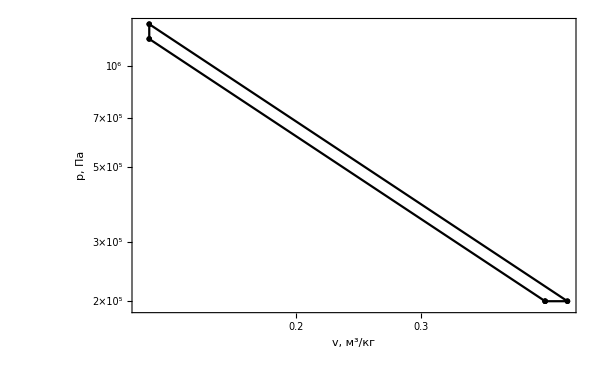

```mathematica
Show[ListPlot[{v,p}ᵀ,ScalingFunctions->{"Log","Log"},Frame->True,ImageSize->600,GridLines->{Automatic,Table[i 10^5,{i,1,100}]},FrameStyle->Thick,GridLinesStyle->Gray,FrameLabel->{"v, (:043c)^3/(:043a:0433)","p, Па"}],ListLinePlot[Append[{v,p}ᵀ,{v[[1]],p[[1]]}],ScalingFunctions->{"Log","Log"}]]
```

б) v – p

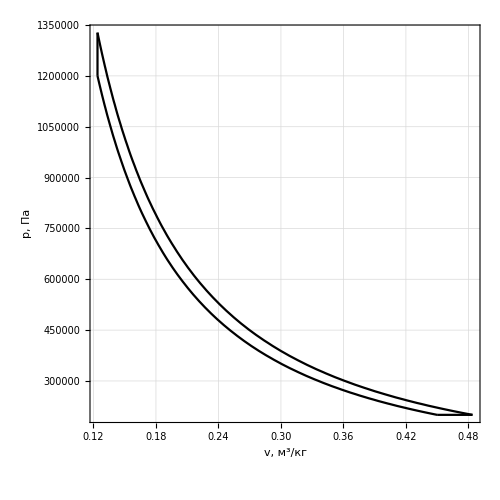

```mathematica
Show[{ContourPlot[P V^k==p[[1]] v[[1]]^k,{V,v[[2]],v[[1]]},{P,p[[1]],p[[2]]},Frame->True,ImageSize->500,PlotRange->All,GridLines->Automatic,FrameStyle->Thick,GridLinesStyle->Gray,FrameLabel->{"v, (:043c)^3/(:043a:0433)","p, Па"}],ContourPlot[V==v[[2]] ,{V,v[[2]]-1,v[[4]]+2},{P,p[[2]],p[[3]]}],ContourPlot[P V^k==p[[3]] v[[3]]^k,{V,v[[3]],v[[4]]},{P,p[[4]],p[[3]]}],ContourPlot[P==p[[4]] ,{V,v[[1]],v[[4]]},{P,p[[1]]-2,p[[4]]+2}]}]
```

в) ΔS - T

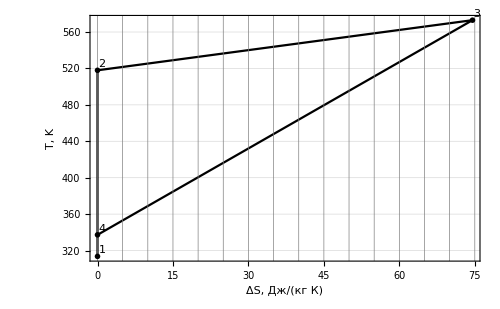

```mathematica
ListLinePlot[{{0,T[[1]]},{0,T[[2]]},{ds[[2]],T[[3]]},{0,T[[4]]}}->{1,2,3,4},Frame->True,ImageSize->500,PlotRange->All,GridLines->{Table[i,{i,0,80,5}],Automatic},FrameTicks->{Table[i,{i,0,80,5}],Automatic},FrameStyle->Thick,GridLinesStyle->Gray,FrameLabel->{"ΔS, (:0414:0436)/(:043a:0433 :041a)","T, K"}]
```

Графическая часть:

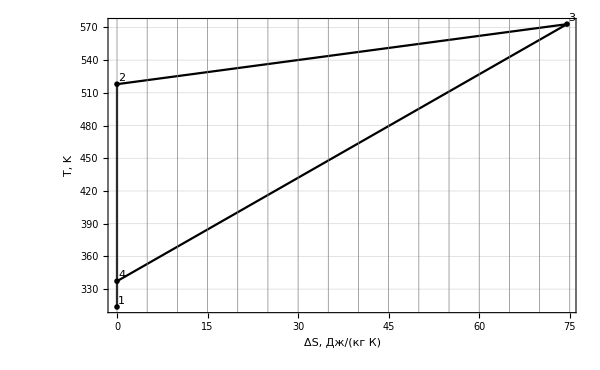

```mathematica
ListLinePlot[{{0,T[[1]]},{0,T[[2]]},{ds[[2]],T[[3]]},{0,T[[4]]}}->{1,2,3,4},Frame->True,ImageSize->600,PlotRange->All,GridLines->{Table[i,{i,0,80,5}],Automatic},FrameTicks->{Table[i,{i,0,80,5}],Automatic},FrameStyle->Thick,GridLinesStyle->Gray,FrameLabel->{"ΔS, (:0414:0436)/(:043a:0433 :041a)","T, K"}]
```